## 慣性モーメントの計算

```mathematica
(*rhoPMMAの密度と質量からをあらかじめ設定して計算*)
ClearAll["Global`*"];
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)
(*正しいとする値*)
rhoPMMA=(1.18(*g/cm^3*))/1000/0.01^3(*kg/cm^3*)
Lx=0.3;(*m*)
Ly=0.42;(*m*)
Lz=0.2;(*m*)
draught=0.1;
rhoBody=500;

massBody=rhoBody*Lx*Ly*Lz;
(*distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];*)
distanceFromAxis[X_,O_,axis_]:=With[{V=X-O,n=Normalize[axis]},
Return[V-Dot[V,n]*n]];
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}];
ans=Solve[rhoPMMA*volume[d]==massBody&&d<Lx/2&&d<Ly/2&&d<Lz/2,d,Reals];
d=d/.ans[[1]](*計算した板厚*);
Print["計算した板厚:",d]

MOI[axis_,d_,rhoPMMA_]:=rhoPMMA*FullSimplify[
Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]
-Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}]
]

Print["密度1.18g/cm^3と質量から計算，{Ixx,Iyy,Izz}=",{MOI[{1,0,0},d,rhoPMMA],MOI[{0,1,0},d,rhoPMMA],MOI[{0,0,1},d,rhoPMMA]}]
```

1180.

計算した板厚:0.0232806

密度1.18g/cm^3と質量から計算，{Ixx,Iyy,Izz}={0.303475,0.196798,0.369273}

```mathematica
Clear[d,rhoPMMA];
(*板厚0.08mmと質量から計算*)
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)
(*正しいとする値*)
Lx=0.3;(*m*)
Ly=0.42;(*m*)
Lz=0.2;(*m*)
draught=0.1;
rhoBody=500;

massBody=rhoBody*Lx*Ly*Lz;
distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}];
d=0.008;
ans=Solve[rhoPMMA*volume[d]==massBody&&d<Lx/2&&d<Ly/2&&d<Lz/2,rhoPMMA,Reals]
rhoPMMA=rhoPMMA/.ans[[1]](*計算した板厚*)
Print["計算したrhoPMMA:",rhoPMMA];
Print["板厚0.08mmと質量から計算した結果，{Ixx,Iyy,Izz}=",{MOI[{1,0,0},d,rhoPMMA],MOI[{0,1,0},d,rhoPMMA],MOI[{0,0,1},d,rhoPMMA]}]
```

{{rhoPMMA→3081.76}}

3081.76

計算したrhoPMMA:3081.76

板厚0.08mmと質量から計算した結果，{Ixx,Iyy,Izz}={0.33201,0.220471,0.40186}

```mathematica
Print["密度が均一とした場合:",
{1/12*rhoBody*Lx*Ly*Lz*(Ly*Ly+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Ly*Ly)}
]
```

密度が均一とした場合:{0.22722,0.1365,0.27972}

## 計算結果

plot2Doption

importData

jsonInfo

/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json

no. | title | length
1 | cpu_time | 439
2 | float_COM | 439
3 | float_EK | 439
4 | float_EP | 439
5 | float_accel | 439
6 | float_area | 439
7 | float_drag_force | 439
8 | float_drag_torque | 439
9 | float_force | 439
10 | float_pitch | 439

3.24503

1.97592

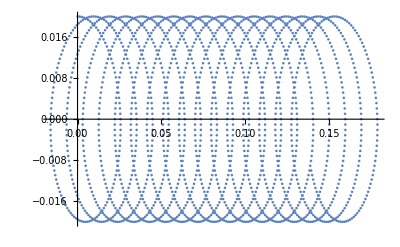

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]

(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/流体力学会2023/Ren2015_H0d04_T1d2_potential_2/result.json"*)

ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
ExperimentData0d04=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
ExperimentData0d04Heave=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_heave.csv"];
ExperimentData0d04Surge=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_surge.csv"];
ExperimentData0d04Pitch=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_pitch.csv"];
name="/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json"
(*name="/Users/tomoaki/BEM/Cheng2018meshC_H0d04_T1d2_piston_with_float_ALE1/result.json";*)
name="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json";
(*name="/Users/tomoaki/BEM/Li_Cheng2018meshB_H0d04_T1d2_piston_positive/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_flap/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential_pahse_shift/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_negative_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_potential_2/result.json"*)

imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
importData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
jsonInfo[name_]:=With[{imported=Import[name,"JSON"]},Grid[Join[{{"no.","title","length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Min[10,Length[imported]]}]],Frame->All,Background->{None,{LightGray,{LightGreen,Green}}}]]
jsonInfo[name]
legend=LineLegend[{"mesh A","mesh B","mesh C","mesh D","mesh E","Exp (Ren et al., 2015)"},LegendMarkerSize->20,LabelStyle->10];
plotstyle={{Red,Dashed},{Blue},{Green,Dashed},{Orange},{Magenta},{Black}};
h=0.4;
d=0.1;
H=0.04;
T=1.2;

w=2π/T;
g=9.81;
Clear[k];
NSolve[w^2==g*k*Tanh[h*k],k,Reals];
k=Abs[k/.%[[1]]]
shift=5.7;

λ=2π*k;
c=Sqrt[g*λ/(2π)*Tanh[2π*h/λ]]
ρ=1000;
a=H/2;
stokesdrift[t_,x_,z_]:={a*w*Cosh[k(z+h)]/Sinh[k*h] Cos[w*t-k*x]+1/2*w*k*a*a*(Cosh[2*k(z+h)]-Cos[2(w*t-k*x)])/Sinh[k*h]^2,-a*w Sinh[k(z+h)]/Sinh[k*h] Sin[w*t-k*x]}
drift=Integrate[stokesdrift[t,0,0],t];
ListPlot[Table[drift,{t,0,20,0.01}],PlotRange->All]
```

## ALEが計算結果に与える影響

```mathematica
(*メッシュが細かくなるに従って，計算結果が収束することを期待していた．しかし，波の運動は早く収束するのだが，浮体の運動は直線的に収束しているようには見えなかった．
浮体周辺のメッシュの細かさが影響するだろうと考え計算したところ，浮体の運動は確かに大きく変化したが，期待する収束方向に変化しなかった．
メッシュの細かさはALEによる修正度合いにも影響を与えるだろうから，これまで確認したメッシュと計算の関係は，実はALEと計算の関係が根本的には決めているのではないかと考えた．
そこで，ALEを適用する頻度N，N time_stepに1度，を変更して計算結果を比較してみる．

ALEはできるだけ少ない方が収束しやすい，のような結果が得られるのではないか．

結果：ALEの頻度は，結果に影響を及ぼさなかった．
慣性モーメントが正しくないためにこのような結果になったと考えられる．
*)
```

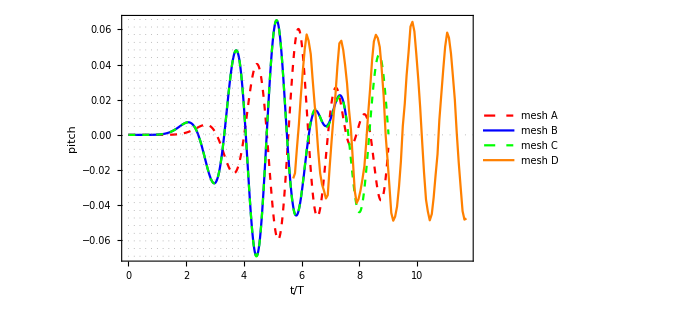

```mathematica
meshAALE1="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston/result.json";
meshAALE3="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE3/result.json";
meshAALE6="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE6/result.json";
ListPlot[
{{importGetData[meshAALE1,"simulation_time"],(importGetData[meshAALE1,"float_pitch"])}ᵀ,
{importGetData[meshAALE3,"simulation_time"],(importGetData[meshAALE3,"float_pitch"])}ᵀ,
{importGetData[meshAALE6,"simulation_time"],(importGetData[meshAALE6,"float_pitch"])}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
PlotStyle->plotstyle,
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

## メッシュの細かさが計算結果に与える影響

```mathematica
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->400,
PlotStyle->{{Blue},{Black},{Red}},
AspectRatio->1/3};
plotxrange={1,13};
(*メッシュと計算の収束*)

meshC="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json"
meshD=meshC;"/Users/tomoaki/BEM/Cheng2018meshD_H0d04_T1d2_piston_with_float_ALE1_saved/result.json"
Dimensions["cpu_time"/.Import[meshC]]
Dimensions["cpu_time"/.Import[meshD]]
```

/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json

/Users/tomoaki/BEM/Cheng2018meshD_H0d04_T1d2_piston_with_float_ALE1_saved/result.json

{439}

{439}

```mathematica
Manipulate[
ListPlot[
{{importGetData[meshC,"float_COM",1],importGetData[meshC,"float_COM",3]-0.4}ᵀ,
{importGetData[meshD,"float_COM",1],importGetData[meshD,"float_COM",3]-0.4}ᵀ,
Table[drift,{t,0,10,0.01}],
(*{importGetData[meshC,"float_COM",1]-shift,importGetData[meshC,"float_COM",3]-0.4}ᵀ,
{importGetData[meshD,"float_COM",1]-shift,importGetData[meshD,"float_COM",3]-0.4}ᵀ,
{importGetData[meshE,"float_COM",1]-shift,importGetData[meshE,"float_COM",3]-0.4}ᵀ,*)
{#1,#2}&@@@ExperimentData0d04},
PlotRange->{{-0.04,0.04},All},
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

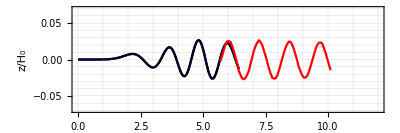

```mathematica
fig=ListPlot[
{{(importGetData[meshC,"simulation_time"]),(importGetData[meshC,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshD,"simulation_time"]),(importGetData[meshD,"float_COM",3]-0.4)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Heave},
Evaluate[opt],
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{{0,12.},{-0.07,0.07}},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

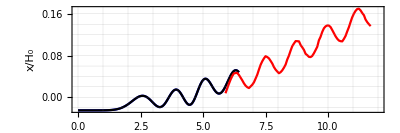

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_COM",1]-3.375)}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,"float_COM",1]-3.375)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Surge},
Joined->{True,True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{{0,12.},Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

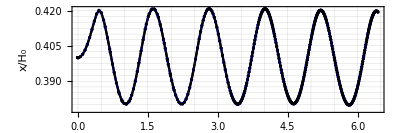
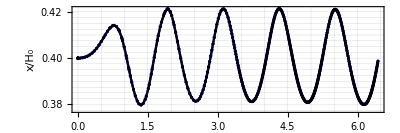
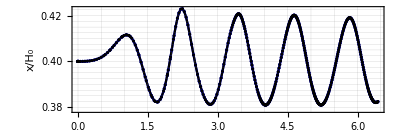
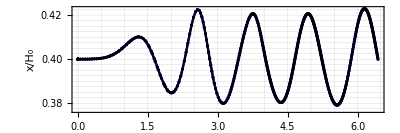

```mathematica
Table[
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,data,3])}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,data,3])}ᵀ},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Mesh->All,
PlotRange->{All,All},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
],{data,{"gauge0_intersection","gauge1_intersection","gauge2_intersection","gauge3_intersection"}}]
```

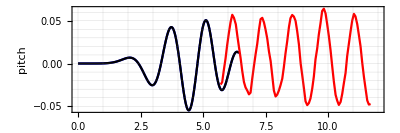

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_pitch"])}ᵀ,
{importGetData[meshD,"simulation_time"],(importGetData[meshD,"float_pitch"])}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{{0,12.},All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

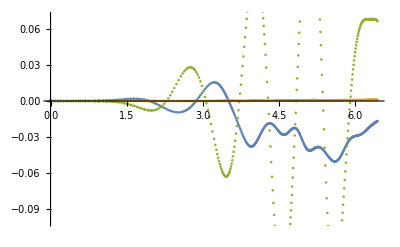

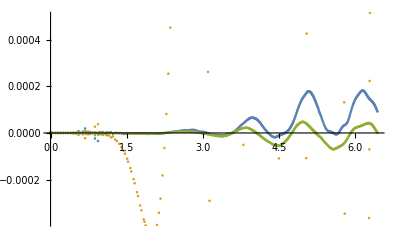

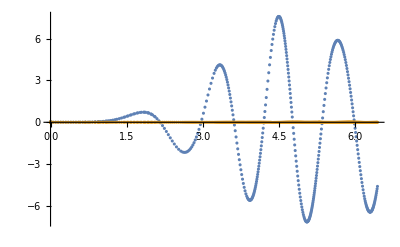

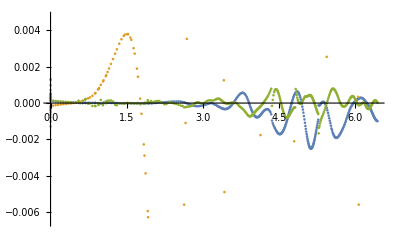

```mathematica
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_force",3])}ᵀ}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_drag_torque",3])}ᵀ}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",2])}ᵀ(*,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_force",3])}ᵀ*)}
]
ListPlot[
{{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",1])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",2])}ᵀ,
{importGetData[meshC,"simulation_time"],(importGetData[meshC,"float_torque",3])}ᵀ}
]
```

## あるケースの結果

```mathematica
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->400,
PlotStyle->{{Blue},(*{Black},*){Red}},
AspectRatio->1/5};
plotxrange={1,12};
```

```mathematica
shift=4.5-1.2
```

3.3

```mathematica
mesh="meshA";
name="/Users/tomoaki/BEM/Cheng2018"<>mesh<>"_H0d04_T1d2_piston_with_float_ALE1/result.json"
```

/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_with_float_ALE1/result.json

```mathematica
Manipulate[
ListPlot[
{{importGetData[name,"float_COM",1],importGetData[name,"float_COM",3]-0.4}ᵀ
(*,{#1,#2}&@@@ExperimentData,*)
(*,Table[drift,{t,0,10,0.01}]*)
,{#1+shift,#2}&@@@ExperimentData0d04},
PlotRange->All,
Joined->{True,True,False},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->16,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

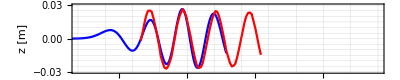

```mathematica
fig=ListPlot[
{{(importGetData[name,"simulation_time"]),(importGetData[name,"float_COM",3]-0.4)}ᵀ,
{T*#1+shift,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True},
PlotRange->{plotxrange,{-0.03,0.03}},
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["z [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_z_Ren2015.jpg"}],%,ImageResolution->150];
```

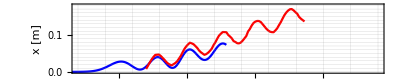

```mathematica
ListPlot[
{{importGetData[name,"simulation_time"],(importGetData[name,"float_COM",1]-3.35)}ᵀ,
{T*#1+shift,h*#2}&@@@ExperimentData0d04Surge},
Joined->{True,True},
PlotRange->{plotxrange,{0,0.18}},
(*PlotRange->{Automatic,Automatic},*)
(*GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},*)
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["x [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_x_Ren2015.jpg"}],%,ImageResolution->150];
```

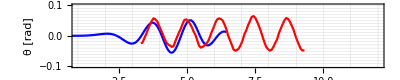

```mathematica
ListPlot[
{{importGetData[name,"simulation_time"],importGetData[name,"float_pitch"]}ᵀ,
{T*#1+shift,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True},
PlotRange->{plotxrange,{-0.1,0.1}},
FrameLabel->{Style["t [s]",FontSize->16,FontFamily->"Times"],Style["θ [rad]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_pitch_Ren2015.jpg"}],%,ImageResolution->150];
```

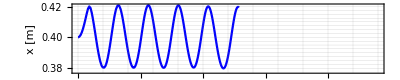
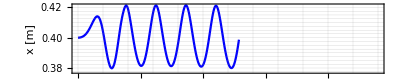
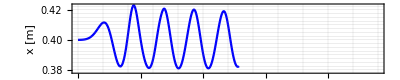
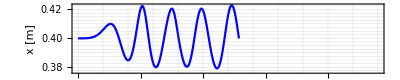

```mathematica
Table[
ListPlot[
{importGetData[name,"simulation_time"],(importGetData[name,data,3])}ᵀ,
Joined->{True,True},
PlotRange->{{0,12},All},
FrameLabel->{(*Style["t [s]",FontSize->16,FontFamily->"Times"]*)None,Style["x [m]",FontSize->16,FontFamily->"Times"]},
Evaluate[opt],
Evaluate[plot2Doption]
],{data,{"gauge0_intersection","gauge1_intersection","gauge2_intersection","gauge3_intersection"}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],mesh<>"_t_vs_elevation_Ren2015.jpg"}],%[[1]],ImageResolution->150];
```